# Quantum circuit into Qiskit

Convert quantum circuit into Qiskit and vice versa

## Example Content

From Wolfram quantum framework, one can directly transform the circuit object into corresponding Qiskit circuit, or find its OPENQASM. You need to configure your system to evaluate external Python code, in order to use Qiskit-related functionalities of Wolfram quantum framework.

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

PacletObject[…]

Create the magic circuit with measurements:

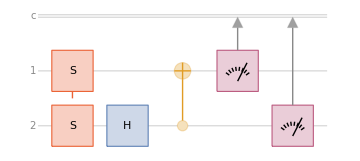

```mathematica
qc=QuantumCircuitOperator[{"S"->{1,2},"H"->2,"CNOT"->{2,1},{1},{2}}];
qc["Diagram"]
```

Make sure that qiskit is installed

```mathematica
ResourceFunction["PythonPackageInstalledQ"]["qiskit"]
```

True

If needed, use ResourceFunction["PythonPackageInstall"]["qiskit"] to install it.

Transform magic circuit to its Qiskit circuit:

```mathematica
qiskit=qc["Qiskit"]
```

QiskitCircuit[…]

Generate its Qiskit diagram:

```mathematica
qiskit["Diagram"]
```

-Graphics-

Generate OPENQASM from Qiskit circuit:

```mathematica
qiskit["QASM"]
```

OPENQASM 2.0;
include "qelib1.inc";
qreg q[2];
creg c[2];
s q[0];
u2(0,-pi/2) q[1];
cx q[1],q[0];
measure q[0] -> c[0];
measure q[1] -> c[1];

Generate corresponding circuit from OPENQASM:

```mathematica
ImportQASMCircuit[qiskit["QASM"]]
```

QiskitCircuit[…]

Transform the Qiskit object back to quantum circuit object:

```mathematica
qiskit["QuantumCircuit"]
```

QuantumCircuitOperator[…]

Generate the outcome of a Qiskit circuit (by default, 1024 shots to find frequency of measurement results):

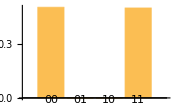

```mathematica
qiskit[]["ProbabilityPlot"]
```

Customize number of shots:

```mathematica
qiskit["Shots"->100]["Probabilities"]
```

<|00→16/25,01→0,10→0,11→9/25|>

Turn the Qiskit object into bytes by specifying a provider and a backend:

```mathematica
BaseEncode@qiskit["QPY","Provider"->"IBMProvider","Backend"->"ibm_perth"]
```

eJwL9Az29gzhZJBkYoAAxkIG7jQGDiCLHYhhokxIbPbkzKLk0swSXUMjAwfRv7tf7l5eWl1byAjWwgjUjwoYkYwAAWYozQKlWaE0WzIjWBUjYzIOE4BqoDxGBuwgKMo9sSQV7II0qBCHhK5LyG/Fn/YkaGZE08x5AKyZAY/m4Ai4ZgosgroSBJgw9YHNdEZYBAlpdmRZLLb5piYWlxZBAiWZVB3guGCEKANpY/8PBCDXFcIiCxbd8OgFy7AysDMm5iVn5uQkQsU5oTQXlOaG0jxQmhfmqEKYy2AmsyMMYkTlMqFymVG5LKhcmI+ZoCpZGCBpjw0A88hFfA==

Let's consider another example, that one will use more features of Qiskit supported in our framework.

Generate a multiplexer circuit:

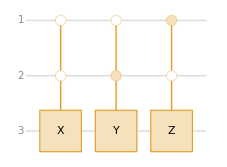

```mathematica
QuantumCircuitOperator[{"Multiplexer","X","Y","Z"}]["Diagram"]
```

Decompose a complex circuit (such as Multiplexer) into simpler ones and return its Qiskit circuit:

```mathematica
QuantumCircuitOperator[{"Multiplexer","X","Y","Z"}]["Qiskit"]["Decompose"]["Diagram"]
```

-Graphics-

Transpile a complex circuit (such as Multiplexer) into simpler ones and return its Qiskit circuit:

```mathematica
transpile=QuantumCircuitOperator[{"Multiplexer","X","Y","Z"}]["Qiskit"]["Transpile"]
```

QiskitCircuit[…]

Transform Qiskit into quantum circuit object and return its diagram:

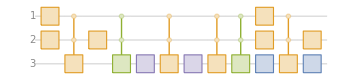

```mathematica
transpile["QuantumCircuit"]["Diagram","ShowGateLabels"->False]
```

## Supporting Data and Definitions

(Your data can be Dataset[…], EntityStore[…], Image[…], Audio[…] or any other expression)

```mathematica
ResourceData[{{}},"NameOfContent"]=xxxx
```

(xxxx can be your data, or File[…], CloudObject[…] or LocalObject[…] that contains it.)

## Thumbnail Image

-Graphics-

## Source & Additional Information

### Contributed By

Wolfram Research, Quantum Computation Framework Team

### Keywords

Quantum circuit

Wolfram quantum framework

Qiskit

### Categories

Algebra
 Calculus
 Complex Systems
 Control Systems
 Engineering
 Food & Nutrition
 Graphs & Networks
 Machine Learning
 Optimization
 Puzzles and Recreation
 System Modeling
 Video Processing
  |  Astronomy
 Cellular Automata
 Computer Science
 Creative Arts
 Finance & Economics
 Geography
 Image Processing
 Mathematics
 Physics
 Signal Processing
 Text & Language Processing
 Visualization & Graphics
 |  Audio Processing
 Chemistry
 Computer Vision
 Data Science
 Finite Element Method
 Geometry
 Life Sciences
 Notebooks & User Interfaces
 Presentation & Publication
 Social Sciences
 Time-Related Computation
 Quantum Computation

### Related Documentation Pages

Symbol name or documentation URI

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

## Author Notes

Additional information about limitations, issues, etc.